# MAPK-Scaffold Model and Simulation

## Preliminary Model

```mathematica
eq={RAF'[t]==k2 RAFpRAFPh[t]-a1 RAF[t] (RAFKtot-RAFRAFKi[t])+d1 RAFRAFKi[t],RAFRAFKi'[t]==a1 RAF[t] (RAFKtot-RAFRAFKi[t])-(d1+k1) RAFRAFKi[t],RAFp'[t]==(d5+k5) MEKpRAFp[t]+(d3+k3) MEKRAFp[t]-a3 MEK[t] RAFp[t]-a5 MEKp[t] RAFp[t]-a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])+d2 RAFpRAFPh[t]+k1 RAFRAFKi[t],RAFpRAFPh'[t]==a2 RAFp[t] (RAFPhtot-RAFpRAFPh[t])-(d2+k2) RAFpRAFPh[t],MEK'[t]==of1 (C2[t]+C6[t]+C9[t])-on1 (C1[t]+C4[t]+C5[t]) MEK[t]+k4 MEKpMEKPh[t]+d3 MEKRAFp[t]-a3 MEK[t] RAFp[t],MEKRAFp'[t]==-(d3+k3) MEKRAFp[t]+a3 MEK[t] RAFp[t],MEKp'[t]==d4 MEKpMEKPh[t]-a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+k6 MEKppMEKPh[t]+d5 MEKpRAFp[t]+k3 MEKRAFp[t]-a5 MEKp[t] RAFp[t],MEKpMEKPh'[t]==-(d4+k4) MEKpMEKPh[t]+a4 MEKp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t]),MEKpRAFp'[t]==-(d5+k5) MEKpRAFp[t]+a5 MEKp[t] RAFp[t],MEKpp'[t]==of3 (C3[t]+C7[t]+C8[t])+(d7+k7) MAPKMEKpp[t]+(d9+k9) MAPKpMEKpp[t]-a7 MAPK[t] MEKpp[t]-a9 MAPKp[t] MEKpp[t]-a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])+d6 MEKppMEKPh[t]+k5 MEKpRAFp[t],MEKppMEKPh'[t]==a6 MEKpp[t] (MEKPhtot-MEKpMEKPh[t]-MEKppMEKPh[t])-(d6+k6) MEKppMEKPh[t],MAPK'[t]==of2 (C4[t]+C6[t]+C7[t])-on2 (C1[t]+C2[t]+C3[t]) MAPK[t]+d7 MAPKMEKpp[t]+k8 MAPKpMAPKPh[t]-a7 MAPK[t] MEKpp[t],MAPKMEKpp'[t]==-(d7+k7) MAPKMEKpp[t]+a7 MAPK[t] MEKpp[t],MAPKp'[t]==k7 MAPKMEKpp[t]+d8 MAPKpMAPKPh[t]+d9 MAPKpMEKpp[t]-a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+k10 MAPKppMAPKPh[t]-a9 MAPKp[t] MEKpp[t],MAPKpMEKpp'[t]==-(d9+k9) MAPKpMEKpp[t]+a9 MAPKp[t] MEKpp[t],MAPKpp'[t]==of4 (C5[t]+C8[t]+C9[t])+k9 MAPKpMEKpp[t]-a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])+d10 MAPKppMAPKPh[t],MAPKpMAPKPh'[t]==-(d8+k8) MAPKpMAPKPh[t]+a8 MAPKp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t]),MAPKppMAPKPh'[t]==a10 MAPKpp[t] (MAPKPhtot-MAPKpMAPKPh[t]-MAPKppMAPKPh[t])-(d10+k10) MAPKppMAPKPh[t],C1'[t]==of1 C2[t]+of3 C3[t]+of2 C4[t]+of4 C5[t]-C1[t] (on2 MAPK[t]+on1 MEK[t]),C2'[t]==of2 C6[t]+of4 C9[t]-C2[t] (of1+on2 MAPK[t])+on1 C1[t] MEK[t]-k5 C2[tuu] RAFp[t],C3'[t]==-of3 C3[t]+of2 C7[t]+of4 C8[t]-on2 C3[t] MAPK[t]+k5 C2[t] RAFp[t],C4'[t]==of1 C6[t]+of3 C7[t]+on2 C1[t] MAPK[t]-C4[t] (of2+on1 MEK[t]),C5'[t]==of3 C8[t]+of1 C9[t]-C5[t] (of4+on1 MEK[t]),C6'[t]==-(of1+of2) C6[t]+on2 C2[t] MAPK[t]+on1 C4[t] MEK[t]-k5 C6[t] RAFp[t],C7'[t]==-k9 C7[t]-of2 C7[t]-of3 C7[t]+on2 C3[t] MAPK[t]+k5 C6[t] RAFp[t],C8'[t]==k9 C7[t]-(of3+of4) C8[t]+k5 C9[t] RAFp[t],C9'[t]==-(of1+of4) C9[t]+on1 C5[t] MEK[t]-k5 C9[t] RAFp[t]};
params={a1->1,a10->5,a2->0.5,a3->3.3,a4->10,a5->3.3,a6->10,a7->20,a8->5,a9->20,C1tot->0,d1->0.4,d10->0.4,d2->0.5,d3->0.42,d4->0.8,d5->0.4,d6->0.8,d7->0.6,d8->0.4,d9->0.6,k1->0.1,k10->0.1,k2->0.1,k3->0.1,k4->0.1,k5->0.1,k6->0.1,k7->0.1,k8->0.1,k9->0.1,MAPKPhtot->0.3,MAPKtot->0.4,MEKPhtot->0.2,MEKtot->0.2,of1->0.05,of2->0.05,of3->0.05,of4->0.5,on1->10,on2->10,RAFKtot->0.2 UnitStep[t],RAFPhtot->0.3,RAFtot->0.3};
tstart=-1000;
ic={RAF[tstart]==RAFtot,RAFRAFKi[tstart]==0,RAFp[tstart]==0,RAFpRAFPh[tstart]==0,MEK[tstart]==MEKtot,MEKRAFp[tstart]==0,MEKp[tstart]==0,MEKpMEKPh[tstart]==0,MEKpRAFp[tstart]==0,MEKpp[tstart]==0,MEKppMEKPh[tstart]==0,MAPK[tstart]==MAPKtot,MAPKMEKpp[tstart]==0,MAPKp[tstart]==0,MAPKpMEKpp[tstart]==0,MAPKpp[tstart]==0,MAPKpMAPKPh[tstart]==0,MAPKppMAPKPh[tstart]==0,C1[tstart]==C1tot,C2[tstart]==0,C3[tstart]==0,C4[tstart]==0,C5[tstart]==0,C6[tstart]==0,C7[tstart]==0,C8[tstart]==0,C9[tstart]==0};
```

```mathematica
len=2;
params=params/.Rule[RAFKtot,_]->Rule[RAFp,0.14]/.C1tot->Stot;
params=Join[params,{p2->0.1,p4->0.1,Di->0.0001}];
params=Flatten[{params,Array[{p1[#]->0.1,p3[#]->0.1}&,len,0]}];
equ=Drop[eq,4];
equ=equ/.RAFp[t]->RAFp;
FluxCM=p1[s]*Scyto[t]-p2*Smem[t];
FluxMV=p3[s]*Smem[t];
FluxVC=p4*C1[t];
equ=equ/.C1'[t]==q_:>C1'[t]==q+(FluxMV-FluxVC);
equ=Join[
{Scyto'[t]==FluxVC-FluxCM},
equ,
{Smem'[t]==FluxCM-FluxMV}];
vars=equ[[All,1]];
vars=vars/.x_'[t]->x;
equ=equ/.Thread[vars->(#[s]&/@vars)];
equ=equ/.v_[s]'[t]==lhs_/;FreeQ[v,C1|C2|C3|C4|C5|C6|C7|C8|C9|Smem]->v[s]'[t]==lhs+Di(v[s-1][t]-2v[s][t]+v[s+1][t]);

equ=Flatten@Table[equ,{s,0,len-1}];
equ=equ/.{x_[-1][t]->x[0][t],x_[len][t]->x[len-1][t]};
vars=equ/.v_'[t]==_->v;
icODE=vars/.{MEK[s_]->MEK[s][0]==MEKtot,MAPK[s_]->MAPK[s][0]==MAPKtot,Scyto[s_]->Scyto[s][0]==Stot,v_[s_]->v[s][0]==0};
equODE=equ;
varODE=vars;

MEKtotequ=StringCases[ToString/@vars,___~~"MEK"~~___]//ToExpression//Flatten//Total;
MEKtotequ+=Sum[C2[s]+C3[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
MAPKtotequ=StringCases[ToString/@vars,___~~"MAPK"~~___]//ToExpression//Flatten//Total;
MAPKtotequ+=Sum[C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s],{s,0,len-1}];
Stotequ=Sum[C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}];

equ=equODE;
equ=DeleteCases[equ,MEK[0]'[t]==_];
equ=Append[equ,len*MEKtot==MEKtotequ];
equ=DeleteCases[equ,MAPK[0]'[t]==_];
equ=Append[equ,len*MAPKtot==MAPKtotequ];
equ=DeleteCases[equ,C1[0]'[t]==_];
equ=Append[equ,len*Stot==Sum[
C1[s]+C2[s]+C3[s]+C4[s]+C5[s]+C6[s]+C7[s]+C8[s]+C9[s]+Scyto[s]+Smem[s],{s,0,len-1}]];
equ=equ/.{x_'[t]->0,x_[t]->x};

tend=5000;
runsimODE[pp___]:=Block[{sol,p=Flatten[{pp}],ic=icODE,dtzero,tol=10^-8,maxiter=30,iter},
iter=Catch[
Do[
sol=NDSolve[Join[equODE,ic]//.p/.params,varODE,{t,0,tend}][[1]];
dtzero=Max@Abs[equODE[[All,2]]//.p/.t->tend/.sol/.params];
If[dtzero<tol,Throw[i]];
ic=vars/.x_[s_]:>x[s][0]==(x[s][tend]/.sol);
,{i,maxiter}]];
Join[{dd->dtzero,runsim$maxiter->(iter/.Null->maxiter)},p,sol]
];
runsim[pp___]:=Block[{sol},
sol=runsimODE[pp];
sol/.f_InterpolatingFunction->f[tend]
]
(*
runsimReinit[p___,s___]:=Module[{},
runsim$init=Thread[{
vars,
vars/.Flatten[{s}]/._->0,
Max[{MEKtot,MAPKtot,Stot}]/.Flatten[{p}]/.params}];
runsim$init=runsim$init[[All,{1,2}]];
]
runsimReinit[];
runsim[p___]:=Module[{sol},
sol=FindRoot[equ/.Flatten[{p}]/.params,runsim$init,MaxIterations->∞,DampingFactor->0.1];
If[
MatchQ[sol,{Rule[_,_?NumberQ]..}],
If[MatchQ[sol,{Rule[_,_?NonNegative]..}],
runsimReinit[p,sol]
],
runsimReinit[p];
];
Join[p,sol]
]
*)
dat=Table[
{s,MAPKpp[0]}/.runsim[p4->0,p2->0,Stot->s,p1[_]->100],
{s,0.192,0.202,0.0001}];
MAXMAPKPP=Max[dat[[All,2]]];
```

```mathematica
savefile="/data/mapk/mapk01.mx";
DeleteFile[savefile];
Save[savefile,{MAXMAPKPP,params,equ,vars,runsim,runsimODE,tend,equODE,icODE,varODE}];
```

DeleteFile::nffil: File not found during DeleteFile["/data/mapk/mapk01.mx"].

```mathematica
Exit[]
```

```mathematica
dat=Table[
{s,MAPKpp[0]}/.runsim[p4->0,p2->0,Stot->s,p1[_]->100],
{s,0.0,2.0,0.01}];
```

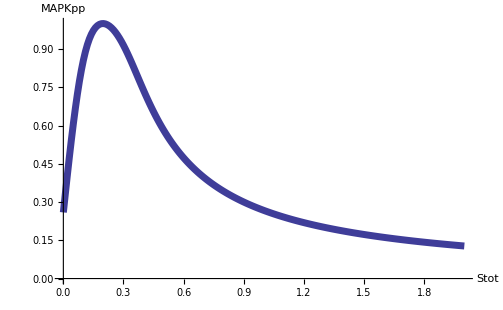

```mathematica
Block[{$TextStyle={"FontSize"->22}},
ListLinePlot[dat/.{s_,m_}->{s,m/MAXMAPKPP},AxesLabel->{"Stot","MAPKpp"},PlotStyle->Thickness[0.01],BaseStyle->{FontSize->14}]
]
```

```mathematica
Get["/data/mapk/mapk01.mx"]
LaunchKernels[]
ParallelEvaluate[$KernelID]
```

5000

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local],KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local],KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
lenX=Range[0.01,1.05,0.05]
lenX=Clip[lenX]
Length[lenX]

grad=Range[0,1.0,0.05]//Chop
Length[grad]
```

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.01}

{0.01,0.06,0.11,0.16,0.21,0.26,0.31,0.36,0.41,0.46,0.51,0.56,0.61,0.66,0.71,0.76,0.81,0.86,0.91,0.96,1.}

21

{0,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

21

```mathematica
{v,θ0}={{p4b, p2, p3a, p3b, p3c, p3d, p3e, p3f, p5, StotNative, StotOpt, StotOE, maxdose, dX}, {6.5, 0.89, 0.00088, 0.48, 110., 0.02, 1.5, 2.1, 7.7, 1.5, 3.3, 42., 0.0085, 0.0001}};
inputθ0[]:=TableForm[Table[With[{i=i},{InputField[Dynamic[θ0[[i]]],Number,FieldSize->{11,1}],
Button["-",θ0[[i]]=0.9*θ0[[i]]],Button["+",θ0[[i]]=1.1*θ0[[i]]],
Button["-",θ0[[i]]=0.99*θ0[[i]]],Button["+",θ0[[i]]=1.01*θ0[[i]]]
}],{i,1,Length[θ0]}],TableHeadings->{v,{"θ0","-10%","+10%","-1%","+1%"}}]
```

```mathematica
tend=10000;
pθ0:=Thread[Rule[v,θ0]]
```

```mathematica
p3sigmoid=Function[s,p3[s]->(p3a+p3b Smem[s][t])((1-p3d)/(1+Exp[(Smem[s][t]-p3e)p3f])+p3d)]/@{0,1};
```

```mathematica
myrunsim[{pp___},OptionsPattern[{lengthX:>lenX,slevel:>({StotNative,StotOE}/.pθ0),gradient:>grad}]]:=With[{p=Flatten[{pp}]},
DistributeDefinitions[θ0];
Transpose@ParallelTable[
plist=Join[p,
{λ->l,Stot->s,γ->g,δ[x_]->g*maxdose(l+dX*x),p1[x_]->p5*δ[x],p3sigmoid,p4[_]->p4b,MI->If[g*dX*maxdose==0,0,(MAPKpp[1]-MAPKpp[0])/(g*dX*maxdose)]}/.p/.pθ0,pθ0];
runsim[plist]
,{l,OptionValue[lengthX]},{s,OptionValue[slevel]},{g,OptionValue[gradient]},Method->"FinestGrained"]
]
```

```mathematica
DistributeDefinitions["Global`*"]
$DistributedContexts=None;
```

{Global`}

## Plots

### Scaffold dose response

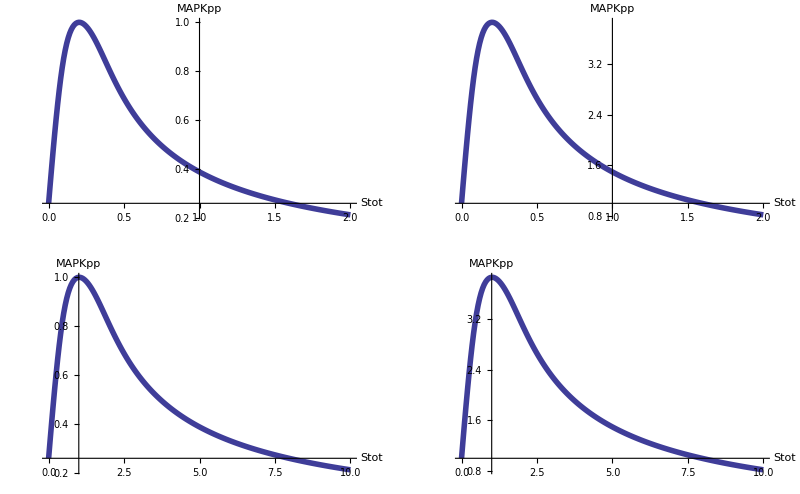

```mathematica
scaffoldDoseResponse=ParallelTable[{s,MAPKpp[0]}/.runsim[p4[_]->0,p2->0,Stot->s,p1[_]->100],{s,0.0,2.0,0.01}];
Table[
ListLinePlot[scaffoldDoseResponse/.{s_,m_}->{s/ss,m/ff},AxesOrigin->{1,scaffoldDoseResponse[[1,-1]]/ff},AxesLabel->{"Stot","MAPKpp"},PlotStyle->Thickness[0.01],BaseStyle->{FontSize->14}],{ss,{1,0.2}},{ff,{MAXMAPKPP,scaffoldDoseResponse[[1,-1]]}}]//GraphicsGrid[#,ImageSize->Full]&
```

## LATEX output